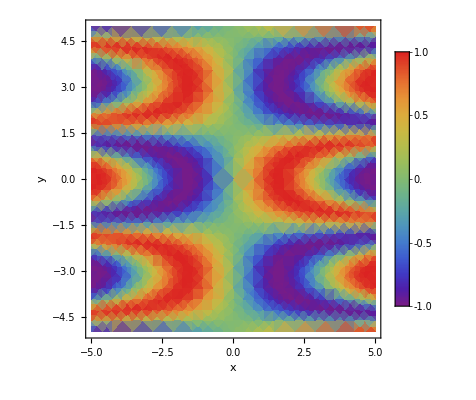

```mathematica
(*定义函数*)f[x_,y_]:=Sin[x Cos[y]]

(*绘制密度图*)
densityPlot=DensityPlot[f[x,y],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"x","y","z = Sin[x Cos[y]]"},PlotRange->All];

(*绘制等值线图*)
contourPlot=ContourPlot[f[x,y]==z,{x,-5,5},{y,-5,5},Contours->Range[-1,1,0.2],FrameLabel->{"x","y"},PlotLegends->Automatic];

(*显示图形*)
Show[densityPlot,contourPlot]
```

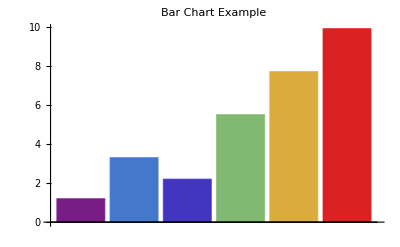
{-Graphics-,-Graphics-}

```mathematica
(*示例数据*)data={1.2,3.3,2.2,5.5,7.7,9.9};

(*绘制棒图*)
barChart=BarChart[data,ChartLabels->Automatic,FrameLabel->{"Index","Value"},PlotLabel->"Bar Chart Example",ColorFunction->"Rainbow"];

(*绘制饼图*)
pieChart=PieChart[data,ChartLabels->Automatic,PlotLabel->"Pie Chart Example",ColorFunction->"Rainbow"];

(*显示图形*)
{barChart,pieChart}
```

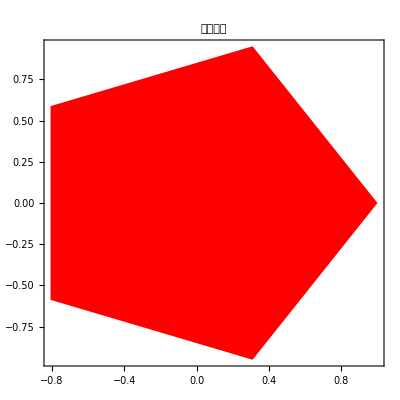

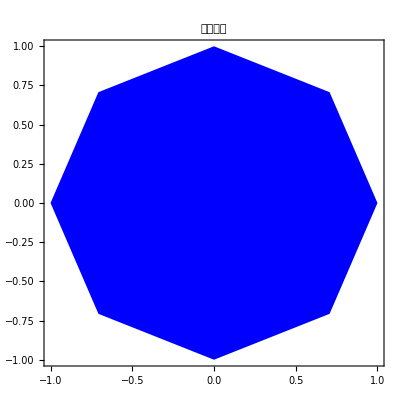

```mathematica
(*定义正五边形的顶点*)pentagonVertices=Table[{Cos[2 Pi k/5],Sin[2 Pi k/5]},{k,0,4}];

(*定义正八边形的顶点*)
octagonVertices=Table[{Cos[2 Pi k/8],Sin[2 Pi k/8]},{k,0,7}];

(*绘制正五边形和正八边形*)
Graphics[{Red,Polygon[pentagonVertices](*正五边形*)},PlotRange->{{-1.5,1.5}},AspectRatio->1,Frame->True,PlotLabel->"正五边形"]

Graphics[{Blue,Polygon[octagonVertices]}  ,PlotRange->{{-1.5,1.5}},AspectRatio->1, Frame->True,PlotLabel->"正八边形"
]
```

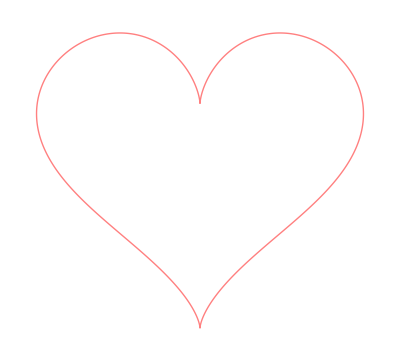

```mathematica
(*心脏线*)heartParam=Table[{16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]},{t,0,2 Pi,0.01}];

(*绘制心脏线*)
heartShape=Graphics[{Pink,Line[heartParam]}];

(*显示图形*)
heartShape
```

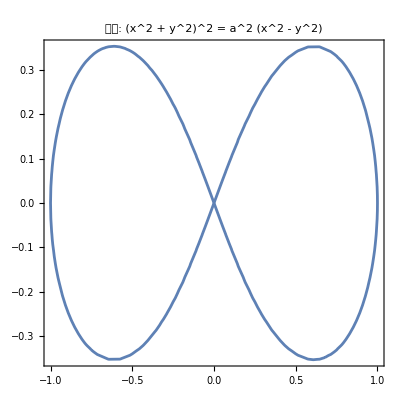

```mathematica
(*定义参数 a*)a=1;

(*绘制曲线*)
curvePlot=ContourPlot[(x^2+y^2)^2==a^2 (x^2-y^2),{x,-2,2},{y,-2,2},Contours->50,PlotRange->All,Axes->True,AspectRatio->1,PlotLabel->"曲线: (x^2 + y^2)^2 = a^2 (x^2 - y^2)"];

(*显示图形*)
curvePlot
```

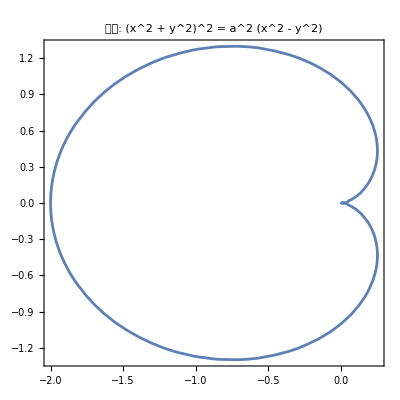

```mathematica
(*定义参数 a*)a=1;

(*绘制曲线*)
curvePlot=ContourPlot[(x^2+y^2)==a (Sqrt[x^2+y^2]-x),{x,-2,2},{y,-2,2},PlotRange->All,Axes->True,AspectRatio->1,PlotLabel->"曲线: (x^2 + y^2)^2 = a^2 (x^2 - y^2)"];

(*显示图形*)
curvePlot
```

```mathematica
(*定义函数*)f[x_]:=x^2  (*可以修改为其他函数*)

(*割线的两个点*)
a=-2; (*左边点*)
b=2;  (*右边点*)

(*动态演示*)
Manipulate[Module[{slope,tangentLine},slope=(f[b]-f[a])/(b-a);(*计算割线的斜率*)tangentLine[x_]:=f[a]+slope (x-a);(*割线方程*)(*绘图*)Plot[{f[x],tangentLine[x]},{x,-3,3},PlotStyle->{Blue,Red},PlotRange->{-1,5},AxesLabel->{"x","y"},PlotLabel->"割线与切线逼近",Epilog->{PointSize[Large],Point[{a,f[a]}],Point[{b,f[b]}]}]],{a,-2,2},(*左边点可移动*){b,a+0.1,3}  (*右边点必须大于左边点*)]
```